# 3D plotting

#### Basic 2D plots

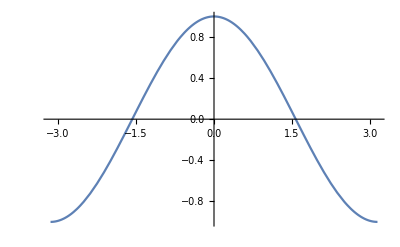

```mathematica
Plot[Cos[t],{t,-π,π}]
```

#### Surface Plots

```mathematica
Plot3D[Cos[t]*y,{t,-π,π},{y,-10,16}]
```

-Graphics3D-

#### Plot Options

```mathematica
Plot3D[Cos[t]*y,{t,-π,π},{y,-10,16},
AxesLabel->{"x_1","x_2","f(x_(1,)x_2)"},
PlotLabel->"f=cos(x_1)x_2",
ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Changing opacity

```mathematica
Plot3D[Cos[t]*y,{t,-π,π},{y,-10,16},
AxesLabel->{"x_1","x_2","f(x_(1,)x_2)"},
PlotLabel->"f=cos(x_1)x_2",
ColorFunction->"Rainbow",
PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
plotsurface=Plot3D[Cos[t]*y,{t,-π,π},{y,-10,16},
AxesLabel->{"x_1","x_2","f(x_(1,)x_2)"},
PlotLabel->"f=cos(x_1)x_2",
ColorFunction->"Rainbow",
PlotStyle->Opacity[1],
FaceGrids->All]
```

-Graphics3D-

#### Fixing view points

```mathematica
Plot3D[Cos[t]*y,{t,-π,π},{y,-10,16},
AxesLabel->{"x_1","x_2","f(x_(1,)x_2)"},
PlotLabel->"f=cos(x_1)x_2",
ColorFunction->"Rainbow",
PlotStyle->Opacity[1],
FaceGrids->All,
ViewPoint->Front]
```

-Graphics3D-

#### Manually specify viewpoint

```mathematica
Plot3D[Cos[t]*y,{t,-π,π},{y,-10,16},
AxesLabel->{"x_1","x_2","f(x_(1,)x_2)"},
PlotLabel->"f=cos(x_1)x_2",
ColorFunction->"Rainbow",
PlotStyle->Opacity[1],
FaceGrids->All,
ViewPoint->{0,-Infinity,0}]
```

-Graphics3D-

### Generating 3D lines

#### Parametric plot 3D

f_x=t
f_y=4t-2
f_z=cos(t)*(4t-2)

```mathematica
ParametricPlot3D[{t,4*t-2,Cos[t]*(4*t-2)},{t,-2,2}]
```

-Graphics3D-

#### Options

```mathematica
plotline=ParametricPlot3D[{t,4*t-2,Cos[t]*(4*t-2)},{t,-2,2},
AxesLabel-> {"x","y","z"},
PlotStyle->{Red,Thickness[0.02]}]
```

-Graphics3D-

```mathematica
Show[plotsurface,plotline]
```

-Graphics3D-

## Generating points using Graphics3D

```mathematica
P={{-2,3,Cos[-2]*3}}
```

{{-2,3,3 Cos[2]}}

#### Create a point object

```mathematica
pt=Point[P]
```

Point[{{-2,3,3 Cos[2]}}]

#### Draw point using Graphics3D

```mathematica
plotpoint=Graphics3D[{AbsolutePointSize[15],Blue,pt}]
```

-Graphics3D-

```mathematica
Show[plotsurface,plotline,plotpoint]
```

-Graphics3D-